## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
Magnetic Lens, v2
```

```mathematica
createWedge[npts_,din_,dout_,θmin1_,θmax1_]:=Module[{},
poly={};
(* initialize constants *)
θmin=θmin1*Pi/180 ;
θmax=θmax1*Pi/180;
dθ=(θmax-θmin)/npts;
poly={};
(* make innner cirlce *)
For[n=0,n≤npts,n++,
θ=θmin+n*dθ;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]]
(* make first connecting line *)
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}];
(* make outer circle *)
For[n=0,n≤npts,n++,
θ=θmax-(θmax-θmin)/npts*n;
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}]];
(* close the polygon *)
θ=θmin;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]
];
```

```mathematica
Nwedge=12;
din=5;
dout=40;
(*zoffset=0;*)
dz=8;
Mr=1;
magmat=RadMatNdFeB[];
makeKstage[KK_,zoff_,ϕrot_,cnt_]:=Module[{},
(* make wedge outlines *)
ϕ=2Pi/Nwedge(1-1/2);
allpolys={};
For[w=1,w≤Nwedge,w++,
createWedge[1,din,dout,360/Nwedge*(w-1),360/Nwedge*w];
AppendTo[allpolys,poly[[1;;-2]]];
ϕ=2Pi/Nwedge(w-1/2);
Mvec=Mr{Cos[KK ϕ],Sin[KK ϕ],0};
rot={{Cos[ϕrot],Sin[ϕrot],0},{-Sin[ϕrot],Cos[ϕrot],0},{0,0,1}};
Mvec=rot.Mvec;
obj=radObjThckPgn[zoff,dz,allpolys[[w]],"z",Mvec];
(*radMatApl[obj,magmat];*)
radObjAddToCnt[cnt,{obj}]
];
];
radUtiDelAll[];
stage=radObjCnt[{}];
(*makeKstage[6,0,Pi/2,stage]
makeKstage[2,10,0,stage]
makeKstage[6,20,Pi/2,stage]
makeKstage[2,30,Pi,stage]
makeKstage[6,40,Pi/2,stage]
makeKstage[2,50,0,stage]
makeKstage[6,60,Pi/2,stage]
makeKstage[2,70,Pi,stage]
makeKstage[6,80,Pi/2,stage]
makeKstage[2,90,0,stage]
makeKstage[6,100,Pi/2,stage]
makeKstage[2,110,Pi,stage]
makeKstage[6,120,Pi/2,stage]*)
piTime =False;
Do[If[EvenQ[i],
If[piTime,
makeKstage[2,i*10,Pi,stage];piTime=False,
makeKstage[2,i*10,0,stage]; piTime=True
],
makeKstage[6, i*10,Pi/2,stage]],{i,1,149}]
```

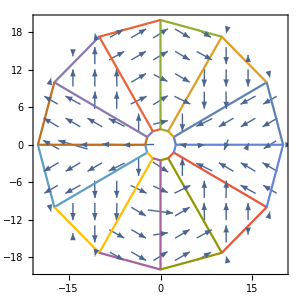

```mathematica
zoff=40;
Mplot=Table[{{x,y},{radFld[stage,"mx",{x,y,zoff}],radFld[stage,"my",{x,y,zoff}]}},{x,-25,25,1},{y,-25,25,1}];
p1=ListVectorPlot[Mplot,AspectRatio->1,ImageSize->300,ColorFunction->"Rainbow",PlotLegends->Automatic];
p2=ListPlot[allpolys,Joined->True];
Show[p1,p2,PlotRange->{{-20,20},{-20,20}}]
```

```mathematica
(* Special options for the Plot[] *)
RadPlot3DOptions[];
(* save the geometry in "dr" *)
dr = radObjDrw[stage];
(* draw the geometry *)
Show[Graphics3D[dr],FrameLabel->{"X","Y","Z"}]
```

-Graphics3D-

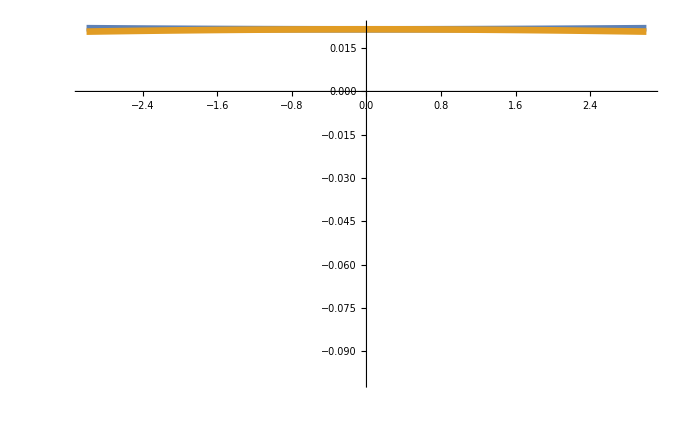

```mathematica
zoffset=0;
xlim=3;
BnormXcut=Table[{x,Sqrt[radFld[stage,"bx",{x,0,zoffset}]^2+radFld[stage,"by",{x,0,zoffset}]^2+radFld[stage,"bz",{x,0,zoffset}]^2]},{x,-xlim,xlim,0.1}];
BnormYcut=Table[{x,Sqrt[radFld[stage,"bx",{0,x,zoffset}]^2+radFld[stage,"by",{0,x,zoffset}]^2+radFld[stage,"bz",{0,x,zoffset}]^2]},{x,-xlim,xlim,0.1}];
ListPlot[{BnormXcut,BnormYcut},Joined->True,PlotStyle->{Thickness[0.007]},PlotRange->{-0.1,All}]
```

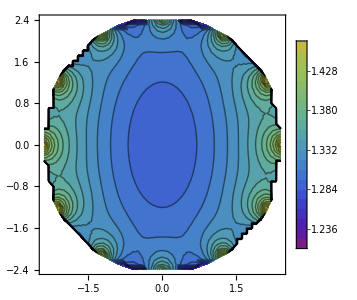

```mathematica
zoff=60;
radiusScan = 2.5;
contourKstage=Table[{x,y,
If[Abs[y]<Sqrt[radiusScan^2-x^2],Sqrt[radFld[stage,"hx",{x,y,zoff}]^2+radFld[stage,"hy",{x,y,zoff}]^2+radFld[stage,"hz",{x,y,zoff}]^2],Infinity]},{x,-radiusScan,radiusScan,0.1},{y,-radiusScan,radiusScan,0.1}];
contourKstage=ArrayReshape[contourKstage,{Dimensions[contourKstage][[1]]*Dimensions[contourKstage][[2]],3}];
ListContourPlot[contourKstage,Contours->20,AspectRatio->1,ImageSize->300,ColorFunction->ColorData[{"Rainbow",{0,1.5}}],PlotLegends->Automatic]
```

```mathematica
xlim=2.5;
ylim=2.5;
zmin=0;
zmax=1500;

BnormXcut=Table[{x,Sqrt[radFld[stage,"bx",{x,0,0}]^2+radFld[stage,"by",{x,0,0}]^2+radFld[stage,"bz",{x,0,0}]^2]},{x,-xlim,xlim,1}];
BnormYcut=Table[{y,Sqrt[radFld[stage,"bx",{0,y,0}]^2+radFld[stage,"by",{0,y,0}]^2+radFld[stage,"bz",{0,y,0}]^2]},{y,-ylim,ylim,1}];
BnormZcut=Table[{z,Sqrt[radFld[stage,"bx",{0,0,z}]^2+radFld[stage,"by",{0,0,z}]^2+radFld[stage,"bz",{0,0,z}]^2]},{z,zmin,zmax,0.1}];
dnormBdz=Differences[BnormZcut[[;;,2]]]/.{x_,y_}->y/x;
dBtab=Table[{BnormZcut[[i,1]],60dnormBdz[[i]]},{i,1,Length[BnormZcut]-1}];
```

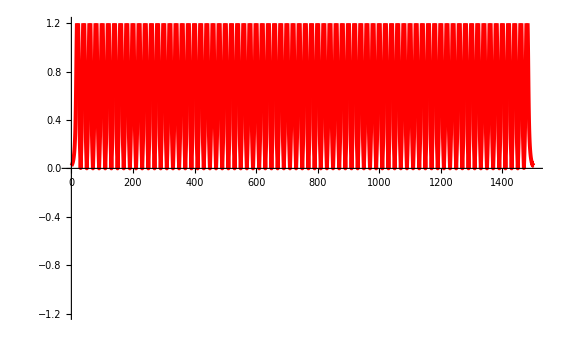

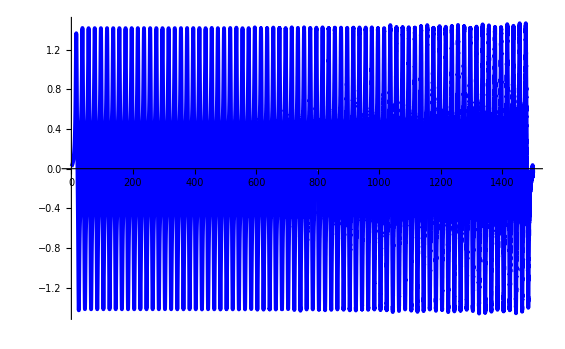

```mathematica
Bplot=ListPlot[BnormZcut,Joined->True,PlotStyle->{Red,Thickness[0.005]},PlotRange->{-1.2,1.2}]
dBplot=ListPlot[dBtab,Joined->True,PlotStyle->{Blue,Thickness[0.005]}]
```

```mathematica
(*contour2D=Table[{Sqrt[radFld[stage,"bx",{x,0,z}]^2+radFld[stage,"by",{x,0,z}]^2+radFld[stage,"bz",{x,0,z}]^2]},{z,-10,130,0.5},{x,-2.5,2.5,0.05}];*)
```

```mathematica
(*ListContourPlot[Transpose[contour2D[[;;,;;,1]]],Contours->25,AspectRatio->0.5,ImageSize->600,ColorFunction->"Rainbow",PlotLegends->Automatic]*)
```

```mathematica
(*zoff = 0;*)
lensStart=0;
lensEnd=1500;
mxy=50;
mz=1500;
```

```mathematica
bMatrix=Table[radFld[stage,"b",{x, y, z}], {x, -din/2, din/2, din/(mxy-1)}, {y, -din/2, din/2, din/(mxy-1)}, {z, lensStart, lensEnd, Abs[lensStart-lensEnd]/(mz-1)}];
normbMatrix=Table[Sqrt[radFld[stage,"bx",{x, y, z}]^2 + radFld[stage,"by",{x, y, z}]^2 +radFld[stage,"bz",{x, y, z}]^2], {x, -din/2, din/2, din/(mxy-1)}, {y, -din/2, din/2, din/(mxy-1)}, {z, lensStart, lensEnd, Abs[lensStart-lensEnd]/(mz-1)}];
SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/zeeman_sisyphus/b_matrix"];
Export["bMatrix_"<>ToString[mz]<>".h5",bMatrix];
Export["normbMatrix_"<>ToString[mz]<>".h5",normbMatrix];
```

## Gradient

### Playing Around with Gradient Implementations

```mathematica
tableOrder=Table[{x^2,y,z},{x,1,3},{y,1,3},{z,1,2}];
test1=Table[x^2 +y^2+z^2,{x,-2, 2,0.8},{y,-2,2,0.8},{z,3,4,0.4}];
```

```mathematica
tableOrder//MatrixForm
tableOrder[[2,All,All]]//MatrixForm
```

((1 | 1 | 1
1 | 1 | 2) | (1 | 2 | 1
1 | 2 | 2) | (1 | 3 | 1
1 | 3 | 2)
(4 | 1 | 1
4 | 1 | 2) | (4 | 2 | 1
4 | 2 | 2) | (4 | 3 | 1
4 | 3 | 2)
(9 | 1 | 1
9 | 1 | 2) | (9 | 2 | 1
9 | 2 | 2) | (9 | 3 | 1
9 | 3 | 2))

((4
1
1) | (4
1
2)
(4
2
1) | (4
2
2)
(4
3
1) | (4
3
2))

```mathematica
tableOrderGradX=Table[If[i≠Dimensions[tableOrder][[1]],
(tableOrder[[i+1,All,All]]-tableOrder[[i,All,All]])(*//MatrixForm*),
(tableOrder[[i,All,All]]-tableOrder[[i-1,All,All]])(*//MatrixForm*)
],
{i,1,Dimensions[tableOrder][[1]]}
]//MatrixForm
```

((3 | 0 | 0
3 | 0 | 0) | (3 | 0 | 0
3 | 0 | 0) | (3 | 0 | 0
3 | 0 | 0)
(5 | 0 | 0
5 | 0 | 0) | (5 | 0 | 0
5 | 0 | 0) | (5 | 0 | 0
5 | 0 | 0)
(5 | 0 | 0
5 | 0 | 0) | (5 | 0 | 0
5 | 0 | 0) | (5 | 0 | 0
5 | 0 | 0))

```mathematica
test//MatrixForm
```

((17.
19.56
22.44) | (14.44
17.
19.88) | (13.16
15.72
18.6) | (13.16
15.72
18.6) | (14.44
17.
19.88) | (17.
19.56
22.44)
(14.44
17.
19.88) | (11.88
14.44
17.32) | (10.6
13.16
16.04) | (10.6
13.16
16.04) | (11.88
14.44
17.32) | (14.44
17.
19.88)
(13.16
15.72
18.6) | (10.6
13.16
16.04) | (9.32
11.88
14.76) | (9.32
11.88
14.76) | (10.6
13.16
16.04) | (13.16
15.72
18.6)
(13.16
15.72
18.6) | (10.6
13.16
16.04) | (9.32
11.88
14.76) | (9.32
11.88
14.76) | (10.6
13.16
16.04) | (13.16
15.72
18.6)
(14.44
17.
19.88) | (11.88
14.44
17.32) | (10.6
13.16
16.04) | (10.6
13.16
16.04) | (11.88
14.44
17.32) | (14.44
17.
19.88)
(17.
19.56
22.44) | (14.44
17.
19.88) | (13.16
15.72
18.6) | (13.16
15.72
18.6) | (14.44
17.
19.88) | (17.
19.56
22.44))

```mathematica
Dimensions[test]
```

{6,6,3}

```mathematica
gradXFiniteDiff=Table[If[i≠Dimensions[test][[1]],
(test[[i+1,All,All]]-test[[i,All,All]])/0.8,
(test[[i,All,All]]-test[[i-1,All,All]])/0.8
],
{i,1,Dimensions[test][[1]]}
];
gradYFiniteDiff=Table[If[i≠Dimensions[test][[2]],
(test[[All,i+1,All]]-test[[All,i,All]])/0.8,
(test[[All,i,All]]-test[[All,i-1,All]])/0.8
],
{i,1,Dimensions[test][[1]]}
];
gradZFiniteDiff=Table[If[i≠Dimensions[test][[3]],
(test[[All,All,i+1]]-test[[All,All,i]])/0.8,
(test[[All,All,i]]-test[[All,All,i-1]])/0.8
],
{i,1,Dimensions[test][[3]]}
];
```

```mathematica
gradXFiniteDiff//MatrixForm
gradYFiniteDiff//MatrixForm
gradZFiniteDiff//MatrixForm
```

((-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2)
(-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (2.22045×10^-15
2.22045×10^-15
0.) | (0.
0.
0.)
(1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6)
(3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2)
(3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2))

((-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2) | (-3.2
-3.2
-3.2)
(-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6) | (-1.6
-1.6
-1.6)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (2.22045×10^-15
2.22045×10^-15
0.) | (0.
0.
0.)
(1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6) | (1.6
1.6
1.6)
(3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2)
(3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2) | (3.2
3.2
3.2))

((3.2
3.2
3.2
3.2
3.2
3.2) | (3.2
3.2
3.2
3.2
3.2
3.2) | (3.2
3.2
3.2
3.2
3.2
3.2) | (3.2
3.2
3.2
3.2
3.2
3.2) | (3.2
3.2
3.2
3.2
3.2
3.2) | (3.2
3.2
3.2
3.2
3.2
3.2)
(3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6)
(3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6) | (3.6
3.6
3.6
3.6
3.6
3.6))

```mathematica
gradFull=Table[{gradXFiniteDiff[[i,j,k]],gradYFiniteDiff[[j,i,k]],gradZFiniteDiff[[k,i,j]]},{i,1,Dimensions[test][[1]]},{j,1,Dimensions[test][[2]]},{k,1,Dimensions[test][[3]]}];
gradFull//MatrixForm
```

((-3.2 | -3.2 | 3.2
-3.2 | -3.2 | 3.6
-3.2 | -3.2 | 3.6) | (-3.2 | -1.6 | 3.2
-3.2 | -1.6 | 3.6
-3.2 | -1.6 | 3.6) | (-3.2 | 0. | 3.2
-3.2 | 0. | 3.6
-3.2 | 0. | 3.6) | (-3.2 | 1.6 | 3.2
-3.2 | 1.6 | 3.6
-3.2 | 1.6 | 3.6) | (-3.2 | 3.2 | 3.2
-3.2 | 3.2 | 3.6
-3.2 | 3.2 | 3.6) | (-3.2 | 3.2 | 3.2
-3.2 | 3.2 | 3.6
-3.2 | 3.2 | 3.6)
(-1.6 | -3.2 | 3.2
-1.6 | -3.2 | 3.6
-1.6 | -3.2 | 3.6) | (-1.6 | -1.6 | 3.2
-1.6 | -1.6 | 3.6
-1.6 | -1.6 | 3.6) | (-1.6 | 0. | 3.2
-1.6 | 0. | 3.6
-1.6 | 0. | 3.6) | (-1.6 | 1.6 | 3.2
-1.6 | 1.6 | 3.6
-1.6 | 1.6 | 3.6) | (-1.6 | 3.2 | 3.2
-1.6 | 3.2 | 3.6
-1.6 | 3.2 | 3.6) | (-1.6 | 3.2 | 3.2
-1.6 | 3.2 | 3.6
-1.6 | 3.2 | 3.6)
(0. | -3.2 | 3.2
0. | -3.2 | 3.6
0. | -3.2 | 3.6) | (0. | -1.6 | 3.2
0. | -1.6 | 3.6
0. | -1.6 | 3.6) | (0. | 0. | 3.2
0. | 0. | 3.6
0. | 0. | 3.6) | (0. | 1.6 | 3.2
0. | 1.6 | 3.6
0. | 1.6 | 3.6) | (2.22045×10^-15 | 3.2 | 3.2
2.22045×10^-15 | 3.2 | 3.6
0. | 3.2 | 3.6) | (0. | 3.2 | 3.2
0. | 3.2 | 3.6
0. | 3.2 | 3.6)
(1.6 | -3.2 | 3.2
1.6 | -3.2 | 3.6
1.6 | -3.2 | 3.6) | (1.6 | -1.6 | 3.2
1.6 | -1.6 | 3.6
1.6 | -1.6 | 3.6) | (1.6 | 0. | 3.2
1.6 | 0. | 3.6
1.6 | 0. | 3.6) | (1.6 | 1.6 | 3.2
1.6 | 1.6 | 3.6
1.6 | 1.6 | 3.6) | (1.6 | 3.2 | 3.2
1.6 | 3.2 | 3.6
1.6 | 3.2 | 3.6) | (1.6 | 3.2 | 3.2
1.6 | 3.2 | 3.6
1.6 | 3.2 | 3.6)
(3.2 | -3.2 | 3.2
3.2 | -3.2 | 3.6
3.2 | -3.2 | 3.6) | (3.2 | -1.6 | 3.2
3.2 | -1.6 | 3.6
3.2 | -1.6 | 3.6) | (3.2 | 2.22045×10^-15 | 3.2
3.2 | 2.22045×10^-15 | 3.6
3.2 | 0. | 3.6) | (3.2 | 1.6 | 3.2
3.2 | 1.6 | 3.6
3.2 | 1.6 | 3.6) | (3.2 | 3.2 | 3.2
3.2 | 3.2 | 3.6
3.2 | 3.2 | 3.6) | (3.2 | 3.2 | 3.2
3.2 | 3.2 | 3.6
3.2 | 3.2 | 3.6)
(3.2 | -3.2 | 3.2
3.2 | -3.2 | 3.6
3.2 | -3.2 | 3.6) | (3.2 | -1.6 | 3.2
3.2 | -1.6 | 3.6
3.2 | -1.6 | 3.6) | (3.2 | 0. | 3.2
3.2 | 0. | 3.6
3.2 | 0. | 3.6) | (3.2 | 1.6 | 3.2
3.2 | 1.6 | 3.6
3.2 | 1.6 | 3.6) | (3.2 | 3.2 | 3.2
3.2 | 3.2 | 3.6
3.2 | 3.2 | 3.6) | (3.2 | 3.2 | 3.2
3.2 | 3.2 | 3.6
3.2 | 3.2 | 3.6))

### Gradient on normbMatrix

```mathematica
Dimensions[normbMatrix]
```

{50,50,1200}

```mathematica
start=1;
stopX=Dimensions[normbMatrix][[1]];
stopY=Dimensions[normbMatrix][[2]];
stopZ=Dimensions[normbMatrix][[3]];
```

```mathematica
gradXNewton=Table[If[i≠stopX,
(normbMatrix[[i+1,All,All]]-normbMatrix[[i,All,All]])/(din/(mxy-1)),
(normbMatrix[[i,All,All]]-normbMatrix[[i-1,All,All]])/(din/(mxy-1))
],
{i,1,stopX}
];
gradYNewton=Table[If[i≠stopY,
(normbMatrix[[All,i+1,All]]-normbMatrix[[All,i,All]])/(din/(mxy-1)),
(normbMatrix[[All,i,All]]-normbMatrix[[All,i-1,All]])/(din/(mxy-1))
],
{i,1,stopY}
];
gradZNewton=Table[If[i≠stopZ,
(normbMatrix[[All,All,i+1]]-normbMatrix[[All,All,i]])/(Abs[lensStart-lensEnd]/(mz-1)),
(normbMatrix[[All,All,i]]-normbMatrix[[All,All,i-1]])/(Abs[lensStart-lensEnd]/(mz-1))
],
{i,1,stopZ}
];
gradNormBFull=Table[{gradXNewton[[i,j,k]],gradYNewton[[j,i,k]],gradZNewton[[k,i,j]]},{i,1,stopX},{j,1,stopY},{k,1,stopZ}];
```

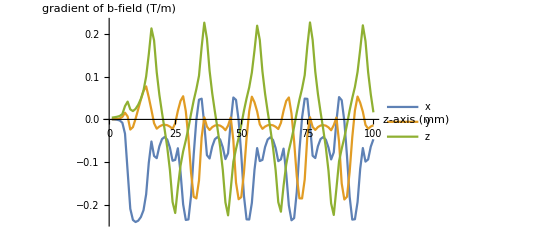

```mathematica
ListPlot[{
gradNormBFull[[15,15,1;;100,1]],
gradNormBFull[[15,15,1;;100,2]],
gradNormBFull[[15,15,1;;100,3]]},
Joined->True,PlotLegends->{"x","y","z"},AxesLabel->{"z-axis (mm)","gradient of b-field (T/m)"}
]
```